# MuRF project PIC functions v3.0

This notebook demonstrates various properties of the MuRF PIC code.
Copyright © Terje B. 2011-2016

```mathematica
(* No need for a long history length eating memory *)
$HistoryLength=1;
(* Clear all previous variable instances *)
ClearAll;
```

```mathematica
potpos=0;
resolution=0;
maxpotpos=10.0;
voltref=5.0;
potposorg=0;
peak=0;
stepsrise=0;
stepsfall=0;
startpos=0;
curvedip =0;
curvepeakrise =0;
curvepeakfall = 0;
voltprsteprise=0;
voltprstepfall=0;
peakposrisefallcurve = 0;
volt=0;
cutoff=0;

GetPlotData[resolutionin_,potposin_, peakposrisefallcurvein_,
curvepeakrisein_, curvepeakfallin_,  curvedipin_, voltrefin_] := Module[{},
curvedata=ConstantArray[0, resolutionin+1];
resolution=resolutionin;
peakposrisefallcurve = peakposrisefallcurvein;
potpos=potposin;
curvedip = curvedipin;
curvepeakrise = curvepeakrisein;
curvepeakfall = curvepeakfallin;
voltref = voltrefin;
potposorg=potpos;

If [potposorg>maxpotpos /2.0, potpos=maxpotpos-potpos];

GetRiseFallStepsAtPotPos[potpos];

stepsrise=(stepsrise * resolution)/100.0;
stepsfall=(stepsfall * resolution)/100.0;

GetCutoffVoltForFallCurve[];
GetPeakPosInResolution[];

If [cutoff>0, startpos=0,startpos=peak-stepsrise];

If [startpos<0, startpos=0];

If[Unequal[peak-startpos, 0],
If [stepsrise==0, 
voltprsteprise=voltref,
voltprsteprise=(voltref-cutoff)/(peak-startpos);
],
voltprsteprise=voltref
];

If [voltprsteprise>voltref, voltprsteprise=voltref];

If [voltprstepfall>voltref, voltprstepfall=voltref];

(* START: This block is for each timer tick in PIC from 0 to resolution *)
For [counter=0,counter<=resolution,counter++,
If [potposorg>maxpotpos/2.0,
volt = GetVoltValue[resolution-counter],
volt = GetVoltValue[counter];
];
curvedata[[counter + 1]] = volt
];
(* END: This block is for each timer tick in PIC from 0 to resolution *)

curvedata
]
```

```mathematica
GetRiseFallStepsAtPotPos[potposin_]:=Module[{},
elements=0.0;
interval=0.0;

 (* Get rise percent *)
	If [potposin≤peakposrisefallcurve,
(
	elements=(peakposrisefallcurve*(resolution/maxpotpos));
interval=Sqrt[curvepeakrise]/elements;
stepsrise=Power[(potposin*(resolution/maxpotpos))*interval,2];
	),
(
	elements=(((maxpotpos/2.0)-peakposrisefallcurve)*(resolution/maxpotpos));
interval=(Sqrt[curvepeakrise]-Sqrt[curvedip])/elements;
stepsrise=Power[Sqrt[curvepeakrise]-
(interval*((potposin-peakposrisefallcurve)*(resolution/maxpotpos))),2];
)
];

 (* Get fall percent *)
If [potposin≤peakposrisefallcurve,
(
	elements=(peakposrisefallcurve*(resolution/maxpotpos));
interval=Sqrt[curvepeakfall]/elements;
stepsfall=Power[(potposin*(resolution/maxpotpos))*interval,2];
	),
(
	elements=(((maxpotpos/2.0)-peakposrisefallcurve)*(resolution/maxpotpos));
interval=(Sqrt[curvepeakfall]-Sqrt[curvedip])/elements;
stepsfall=Power[Sqrt[curvepeakfall]-
(interval*((potposin-peakposrisefallcurve)*(resolution/maxpotpos))),2];
)
];
]
```

```mathematica
GetPeakPosInResolution[]:=Module[{},
peak=(potpos^2/(maxpotpos / 2.0)) * (resolution / maxpotpos)
]
```

```mathematica
GetCutoffVoltForFallCurve[]:=Module[{},
If [stepsfall == 0, voltprstepfall=voltref,voltprstepfall=voltref/stepsfall];

If[voltprstepfall >voltref, voltprstepfall = voltref];

If[resolution-peak-stepsfall<0,
cutoff=Abs[resolution - peak  - stepsfall] * voltprstepfall,
cutoff=0
]
]
```

```mathematica
GetVoltValue[resolutionpos_]:=Module[{},
If[resolutionpos<startpos,
volt=0,
{
If [resolutionpos<peak,
volt=(cutoff+(voltprsteprise*(resolutionpos-startpos)))^2/voltref,
{
If[resolutionpos≤peak+stepsfall,
volt=(voltref-(voltprstepfall*(resolutionpos-peak)))^2/voltref,
volt=0
]
}
];

If [resolutionpos==Round[peak]&&volt<=voltref, volt=voltref]
 }
];

volt
]

GetRiseFallStepsCurves[]:=Module[{},
arraypos=1;
counter= 0;
curvedatarise=ConstantArray[0, Ceiling[((maxpotpos/2.0)*maxpotpos)+1]];
curvedatafall=ConstantArray[0, Ceiling[((maxpotpos/2.0)*maxpotpos)+1]];

For [counter=0,counter≤maxpotpos/2.0,counter+=0.1,
(
GetRiseFallStepsAtPotPos[counter];
curvedatarise[[arraypos]]=Which[stepsrise<0 , 0,stepsrise>=0, stepsrise];
curvedatafall[[arraypos]]=Which[stepsfall<0 , 0,stepsfall>=0,stepsfall];
arraypos += 1
)
];

{curvedatarise, curvedatafall}
]
```

Test the module:

{1.24573,127.188,68.4739,32.,0,100,4,4,0.310367,1.0828}

{2.3268,127.188,68.4739,32.,0,100,4.,6,1.0828,1.0828}

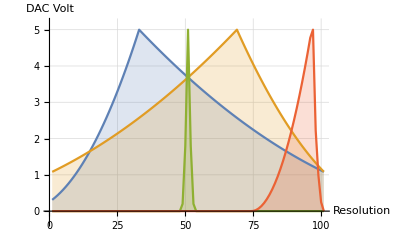
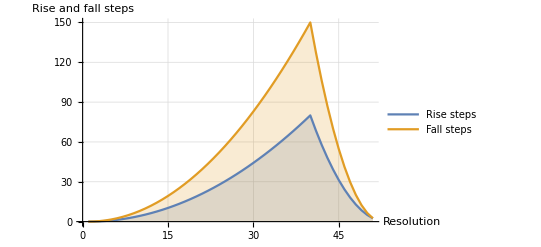

```mathematica
murfcurve1 = GetPlotData[100, 4, 3.9, 80, 150, 2.5, 5.0];
{cutoff, stepsfall, stepsrise, peak, startpos, resolution, potpos, potposorg, murfcurve1[[1]], murfcurve1[[resolution+1]]}

murfcurve2 = GetPlotData[100, 6, 3.9, 80, 150, 2.5, 5.0];
{cutoff, stepsfall, stepsrise, peak, startpos, resolution, potpos, potposorg, murfcurve2[[1]], murfcurve2[[resolution+1]]}

murfcurve3 = GetPlotData[100, 5, 3.9, 80, 150, 2.5, 5.0];

murfcurve4 = GetPlotData[100, 8.5, 3.9, 80, 150, 2.5, 5.0];

mplot1 = Show[ListLinePlot[{murfcurve1,murfcurve2,murfcurve3,murfcurve4},
PlotRange->{{0, resolution+1}, {-0.3, voltref+0.2}},
Filling->Axis,
GridLines->Automatic, GridLinesStyle->LightGray,ImageSize->Scaled[.50],
 AxesLabel->{"Resolution", "DAC Volt"}]];

{curvedatarise, curvedatafall}=GetRiseFallStepsCurves[];

mplot2 = Show[ListLinePlot[{curvedatarise, curvedatafall},
PlotRange->{{0, Ceiling[((maxpotpos/2.0)*maxpotpos)+1]},
{-0.3,Max[Max[curvedatafall],Max[curvedatarise]]}},
Filling-> Axis,
GridLines->Automatic, GridLinesStyle->LightGray,ImageSize->Scaled[.50],
 AxesLabel->{"Resolution", "Rise and fall steps"}, PlotLegends->{"Rise steps", "Fall steps"}]];

Grid[{{mplot1}, {mplot2}}, Frame->All]
```

Animate and control the MuRF module with the MANIPULATE command:

```mathematica
Manipulate[
murfcurve = GetPlotData[theResolution, envelopePos, peakPosRiseFallCurve,
elementsRiseCurve, elementsFallCurve,  curveDip, voltRef];

mplot1 = Show[ListLinePlot[murfcurve,  PlotStyle->Blue, GridLines->Automatic, 
GridLinesStyle->LightGray, PlotRange->{{0, theResolution + 2}, {-0.5, Ceiling[voltRef] + 0.2}},
 Filling->Axis, PlotMarkers->Automatic],
AspectRatio->.35, ImageSize->Scaled[.98], AxesLabel->{"Resolution", "DAC Volt"},
AxesStyle->Directive[Blue,14], TicksStyle->Directive[Blue,10],
AxesOrigin->{0, -0.5}];

{curvedatarise, curvedatafall}=GetRiseFallStepsCurves[];

mplot2 = Show[ListLinePlot[{curvedatarise, curvedatafall},
PlotRange->{{0, Ceiling[((maxpotpos/2.0)*maxpotpos)+1]},
{-0.3, Max[Max[curvedatafall],Max[curvedatarise]]}},
GridLines->Automatic, GridLinesStyle->LightGray,ImageSize->Scaled[.70],
 AxesLabel->{"Resolution", "Rise and fall steps"}, PlotLegends->{"Rise steps", "Fall steps"}, Filling->Axis]];

If[showPlotData, data = {{mplot1},{murfcurve},{mplot2}}, data ={{ mplot1},{mplot2}}];

Grid[data, ItemSize->{{46}}, Spacings->{0.5, 1.5}, Frame->All],
(* NOTE: theResolution = envelopePos = 5 creates curve problem *)
Delimiter, Style["Properties", Bold],
{{voltRef, 5.0, "Max volt out"}, 1, 15, .1, Appearance->"Labeled"},
{{peakPosRiseFallCurve, 3.8, "Peak rise/fall curve"}, 0.1, 4.9, .1, Appearance->"Labeled"},
{{elementsRiseCurve, 90, "Elements rise curve"}, 1, 250, 1, Appearance->"Labeled"},
{{elementsFallCurve, 150, "Elements fall curve"}, 1, 250, 1, Appearance->"Labeled"},
{{curveDip, 2.5, "Curve dip rise/fall curve"}, 0.1,
Min[{elementsRiseCurve,  elementsFallCurve}], .1, Appearance->"Labeled"},
{{theResolution, 50, "Max Elements"}, 6, 160, 1, Appearance->"Labeled"},
{{envelopePos, 0.0, "Envelope Position"}, 0.0, 10, 0.010, Appearance->"Open"},
Delimiter, Style["Display", Bold],
{{showPlotData, True, "Display plot data"}, {True, False} , Appearance->"Labeled"},
ControlPlacement->Top,
 SaveDefinitions->True
]
```